```mathematica
(4.17/10)^-1*20
```

47.9616

```mathematica
48*5/6
```

40

```mathematica
40*5/4.
```

50.

```mathematica
0.1*50
```

5.

```mathematica
((3.25+3+3)/4)/3
```

0.770833

```mathematica
40/0.8
```

50.

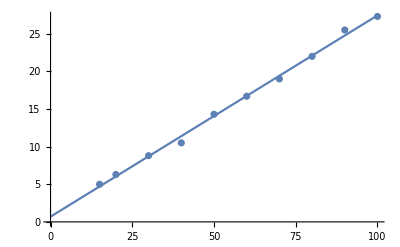

```mathematica
speed = {1.5,2,3,4,5,6,7,8,9,10}*10;
overshoot={5,6.3,8.8,10.5,14.3,16.7,19,22,25.5,27.3};

funct[x_]=Fit[Transpose[{speed,overshoot}],{1,x},x];
Show[
ListPlot[Transpose[{speed,overshoot}]],
Plot[funct[x],{x,0,100}]
]
```

```mathematica
funct[x]
```

0.695302+0.267472 x

```mathematica
Total[{27,27,29,27,27,27}]/6.
```

27.3333

-11.8876+0.372714 x+0.00207748 x^2

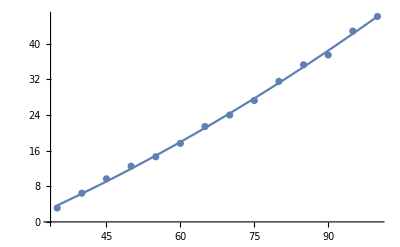

```mathematica
speed = Table[35+i,{i,0,100-35,5}];
spr = {19.2,9.3,6.2,4.8,4.1,3.4,2.8,2.5,2.2,1.9,1.7,1.6,1.4,1.3};
rpm = 1/spr*60;
data = Transpose[{speed,rpm}];
func[x_]=Fit[data,{1,x,x^2},x]
Show[
ListPlot[data],
Plot[func[x],{x,35,100}]
]
```

```mathematica
Solve[r == 1/s*60,s]
```

{{s→60/r}}

```mathematica
t2mEXTEND = {
(*20*){2.452,2.352,2.402,2.352,2.402,2.402,2.402,2.452,2.452,2.552},
(*30*){},
(*40*){},
(*50*){},
(*60*){},
(*70*){},
(*80*){},
(*90*){},
(*100*){}
}

t2mRETRACT= {
(*20*){3.152,3.002,2.902,2.802,2.702,2.702,2.652,2.702,2.702,2.752,2.902},
(*30*){},
(*40*){},
(*50*){},
(*60*){},
(*70*){},
(*80*){},
(*90*){},
(*100*){}
}
```